## Import Raw Data

```mathematica
rawCoordinates = Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/ProcessedCoordinates/rawCoordinates.mx"];
```

```mathematica
rawCoordinates2=rawCoordinates/.Missing[]->Indeterminate;
```

## List of distances

### Import pair name data

```mathematica
PairNames=Table[StringJoin[ToString[a],"and",ToString[b],".mx"],{a,1,Length[rawCoordinates2]},{b,a+1,Length[rawCoordinates2]}];
flatPairNames=Flatten[PairNames];
```

```mathematica
dataDirectory="/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData";
```

```mathematica
currentPairData=Import[FileNameJoin[{dataDirectory,flatPairNames[[1]]}]];
```

### Implement for one pair

Make a list for each pair that has True or False if they are associated for each time step.
- Split at each point where the larger threshold is crossed
- lists that contain values below the smaller threshold are considered connected
- Join back and make clusters, omitting missing sheep

Split behind each Indeterminate group
Split groups based on below or above 50
Rejoin inner layer

```mathematica
testSplit=Catenate/@Split[Split[currentPairData,( #1≤50&&#2≤50||#1>50&&#2>50||#2===Indeterminate&)],With[{first=DeleteCases[#1,Indeterminate],second=DeleteCases[#2,Indeterminate]},first\[VectorLessEqual]50&&second\[VectorLessEqual]50||first\[VectorGreater]50 &&second\[VectorGreater]50]&];
```

```mathematica
testListResult=MemberQ[#,_?(Function[x,x<30])]&/@testSplit;
```

```mathematica
testFinalAssociation=Catenate[MapIndexed[Table[testListResult[[First[#2]]],Length[#1]]&,testSplit]];
```

### Turn into function

```mathematica
determineConnections[pair_,{r1_,r2_}]:=
Module[{split,testList,final},
split=
Catenate/@Split[Split[pair,( #1≤r2&&#2≤r2||#1>r2&&#2>r2||#2===Indeterminate&)],With[{first=DeleteCases[#1,Indeterminate],second=DeleteCases[#2,Indeterminate]},first\[VectorLessEqual]r2&&second\[VectorLessEqual]r2||first\[VectorGreater]r2 &&second\[VectorGreater]r2]&];
testList=MemberQ[#,_?(Function[x,x<r1])]&/@split;
final =Catenate[MapIndexed[Table[testList[[First[#2]]],Length[#1]]&,split]]
]
```

```mathematica
determineConnections[currentPairData,{30,50}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,210299,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}
 |  |  |  |

## Run it on everything

```mathematica
allPairData=Map[Import[FileNameJoin[{dataDirectory,#}]]&,PairNames,{2}];
```

```mathematica
allPairData=Import["/Users/katjad/Documents/Github/SheepCapstone/MXs/DistanceData/allPairData.mx"];
```

### Run on 100 time steps

```mathematica
MostPairData=allPairData[[All,All,700;;800]];
```

Run on just the 100 time steps

```mathematica
testcons=Transpose[Catenate[Map[determineConnections[#,{30,50}]&,MostPairData,{2}]]];
```

Generate all possible edges

```mathematica
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,PairNames,{2}]];
```

Show the first 5 networks that were generated

```mathematica
symmetricalStickyDBSCAN[data_,{r1_,r2_},{tmin_:1,tmax_:210351},rawCoordinates_:rawCoordinates]:=
Module[{cons,allEdges},
cons=Transpose[Catenate[Map[determineConnections[#,{r1,r2}]&,data[[All,All,tmin;;tmax]],{2}]]];
allEdges=UndirectedEdge@@@Catenate[MapIndexed[{#2[[1]],Total[#2]}&,PairNames,{2}]];
MapIndexed[ConnectedComponents[Graph[Flatten[Position[rawCoordinates[[All,tmin-1+First[#2]]],{_?NumericQ,_?NumericQ}]],Pick[allEdges,#1]]]&,cons]]
```

```mathematica
Flatten[Position[rawCoordinates[[All,1]],{_?NumericQ,_?NumericQ}]]
```

{5,8,17,21,22,33,35,38,40,44,48}

```mathematica
symmetricalStickyDBSCAN[MostPairData,{30,50},{1,3}]
```

{{{23,4,5,13,29,35,44,45,6,46},{2,1,10,11,17,22,27,40,41},{24,18,25,34,37,39,42},{38,9,21,36,48},{12,8,32,33},{3,7,20},{47,51}},{{6,4,35,44,45,46,5,13,23,29},{1,2,11,22,27,10,17,40,41},{24,18,25,34,37,39,42},{38,9,21,36,48},{12,8,32,33},{3,7,20},{47,51},{16},{19},{14},{26},{31}},{{23,4,5,13,29,35,44,45,6,46},{1,2,11,22,27,10,17,40,41},{24,18,25,34,37,39,42},{38,9,21,36,48},{12,8,32,33},{3,7,20},{47,51},{16},{14},{26},{31}}}

```mathematica
DBSCAN30Sticky50LonelySheep=symmetricalStickyDBSCAN[allPairData,{30,50},{1,210351}];
```

```mathematica
DBSCAN30Sticky50LonelySheep[[1]]
```

{{38,5,8,17,21,22,33,35,40,44,48},{15},{16},{25},{7},{28},{34},{29},{39},{20},{37},{50},{9},{43},{46},{32},{41},{4},{51},{13},{19},{27},{30},{3},{42},{45},{11},{14},{26},{47},{10},{12},{49},{18},{24},{36},{31},{1},{2},{6},{23}}

## Plot Results

```mathematica
FindRulesFromTo[first_,second_,firstindex_,threshold_]:=
Module[{r},
r=Reap[
Table[If[(Length[c1]-Length[Complement[c1,c2]])/Length[c1]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]];If[(Length[c2]-Length[Complement[c2,c1]])/Length[c2]>threshold,
Sow[{c1,firstindex}->{c2,firstindex+1}]],{c1,first},{c2,second}]];
If[Flatten[DeleteCases[r,{Null},2]]==={},{},DeleteDuplicates[r[[2,1]]]
]]
```

```mathematica
FindFissionFusionGraph[tmin_,tmax_,threshold_,lonelySheep_]:=Graph[Catenate[Table[FindRulesFromTo[lonelySheep[[a]],lonelySheep[[a+1]],a,threshold],{a,tmin,tmax}]]]
```

```mathematica
coloredGraph[g_,enlargingFactor_]:=HighlightGraph[Graph[g,VertexSize->(#->Length[First[#]]*enlargingFactor&/@VertexList[g]),VertexCoordinates->(#->{Last[#]/10,Mean[DeleteMissing[rawCoordinates[[#[[1]],Last[#],2]]]]/100}&/@VertexList[g]),Frame->True,FrameTicks->True,EdgeShapeFunction->"Line",FrameLabel->{Style["Time in min since the start of data collection",Large],None}],ConnectedComponents[UndirectedGraph[Subgraph[g,Select[VertexList[g],VertexDegree[g,#]===2&]]]]]
```

```mathematica
graph30Sticky50=FindFissionFusionGraph[700,800,0.8,DBSCAN30Sticky50LonelySheep];
```

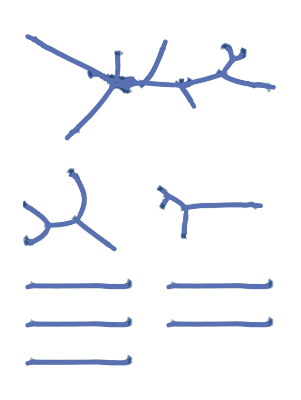

```mathematica
graph30Sticky50
```

```mathematica
coloredGraph[graph30Sticky50,10]
```

```mathematica
DBSCAN30Sticky50LonelySheep[[;;2]]
```

{{{38,5,8,17,21,22,33,35,40,44,48},{15},{16},{25},{7},{28},{34},{29},{39},{20},{37},{50},{9},{43},{46},{32},{41},{4},{51},{13},{19},{27},{30},{3},{42},{45},{11},{14},{26},{47},{10},{12},{49},{18},{24},{36},{31},{1},{2},{6},{23}},{{38,2,3,4,5,7,8,9,10,11,12,14,16,17,18,19,20,21,22,23,24,25,26,27,29,31,33,34,35,36,37,39,40,41,42,44,45,46,47,48,51},{15},{28},{50},{43},{32},{13},{30},{49},{1},{6}}}